# Unanchored Double Pendulum Equations of Motion

An attempt.

-Graphics-

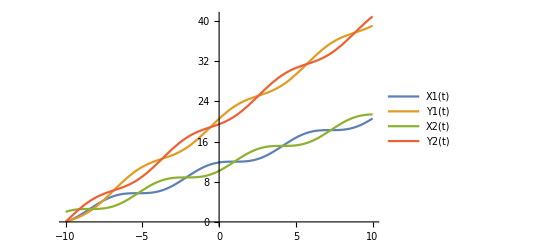

```mathematica
MyNormSquared[{x_,y_}] := x^2+y^2
x1[t] ;(* first coordinate of link 1 *)
y1[t]; (* second coordinate of link 1 *)
theta1[t];  (*Angle from horizontal to first link*)
theta2[t]; (*Angle from horizontal to second link*)
(* Initial Conditions*)
t0 = -10; (*Initial Time*)
InitialConditions = {
x1[t0] == 0,
x1'[t0] == 1,
y1[t0] == 0,
y1'[t0] == 1,
theta1[t0] == 0,
theta1'[t0] == 1,
theta2[t0] == 0,
theta2'[t0] == 1};
(**)
r1 = 1;
r2 = 1;
m1 = 1; 
m2 = 1;
J1 = 1;
J2 = 1;
P1[t]= {x1[t], y1[t]};
theta[t] = {theta1[t],theta2[t]};
x2[t]=x1[t] + r1 Cos[theta1[t]] + r2 Cos[theta2[t]];(* first coordinate of link 2 *)
y2[t] = y1[t] + r1 Sin[theta1[t]]+r2 Sin[theta2[t]];(* second coordinate of link 2 *)
P2[t] = {x2[t],y2[t]};

 KEx[t] = (1/2) m1 MyNormSquared[D[P1[t],t]];
 KEy[t] = (1/2) m2  MyNormSquared[D[P2[t],t]];
KErot[t] = (1/2) (J1 D[theta1[t],t]^2 + J2 D[theta2[t],t]^2);
 KET[t] = KEy[t] + KEx[t] + KErot[t];
 Lagrangian[t] = KET[t];
EOM1[t] = {D[D[Lagrangian[t],x1'[t]],t] - D[Lagrangian[t],x1[t]], D[D[Lagrangian[t],y1'[t]],t] - D[Lagrangian[t],y1[t]], D[D[Lagrangian[t],theta1'[t]],t] - D[Lagrangian[t],theta1[t]],D[D[Lagrangian[t],theta2'[t]],t] - D[Lagrangian[t],theta2[t]]};
EOM[t] = Simplify[EOM1[t]];
DSolve[EOM[t] == {0,0,0,0}, {x1[t],y1[t],theta1[t],theta2[t]},t];
Sol = NDSolve[{EOM[t] == {0,0,0,0},InitialConditions},{x1[t],y1[t],theta1[t],theta2[t]},{t,-10,10},Method->{"EquationSimplification"->"Solve"}];
X2[t] = x1[t] + r1 Cos[theta1[t]] + r2 Cos[theta2[t]] /. Sol;
Y2[t] = y1[t] + r1 Sin[theta1[t]]+r2 Sin[theta2[t]]/. Sol;
X1[t] = x1[t] /. Sol;
Y1[t] = y1[t] /. Sol;
ParametricPlot[{X1[t],Y1[t]},{t,-10,10}]
Plot[{X1[t],Y1[t],X2[t],Y2[t]},{t,-10,10},PlotLegends->"Expressions"]

(*Animate[Graphics[{{PointSize[.025],{Red,Point[{x1[t],y1[t]}]},{Blue,Point[{x2[t],y2[t]}]},Line[{{0,0},{x1[t],y1[t]},{x2[t],y2[t]}}]}/.soldp,{Gray,Line[Map[Function[Evaluate[{x2[#],y2[#]}/.soldp]],Range[0,t,0.025]]]}},PlotRange->{{-2,2},{-2,0}},Axes->True,Ticks->False,ImageSize->500],{t,0,10,.025},SaveDefinitions->True]*)
```

```mathematica
Quit
Remove["Global`*"]
ClearAll
```

ClearAll